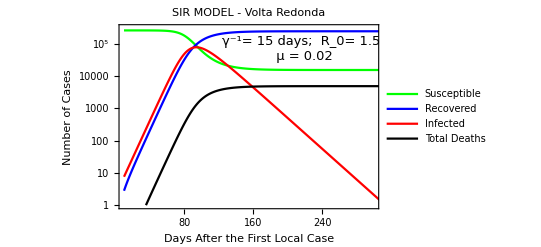

```mathematica
SIR MODEL

Clear[γ,β,R0,pop,solution,Sus,Inf,Rec,Death]
Needs["PlotLegends`"]
γ=1/15;
β=γ*R0;
μ=0.02;
R0=3.0;
pop=257000;
solution=NDSolve[{Sus'[t]==-β*Inf[t]*Sus[t]/pop,Inf'[t]==β Inf[t] Sus[t]/pop-γ Inf[t],Rec'[t]==γ Inf[t],Death[t]==μ*( Rec[t]),Sus[0]==pop,Inf[0]==2,Rec[0]==0,Death[0]==0},{Inf,Sus,Rec,Death},{t,-50,700}];





LogPlot[Evaluate[{Sus[t],Rec[t],Inf[t],Death[t-6]}/.%],{t,10,700},PlotRange->{{10,300},{1,300000}},PlotPoints->640,PlotLegends->Placed[{"Susceptible","Recovered","Infected","Total Deaths"},{0.48,0.27}],GridLines->Automatic,PlotStyle->{{Green},{Blue},{Red},{Black}},TicksStyle->Directive[FontSize-> 15],Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[Black,12],Epilog->Text[Style["γ^-1= 15 days;  R_0= 1.5\n  μ = 0.02",13],Scaled[{0.7,0.87}]],PlotLabel->"SIR MODEL - Volta Redonda",FrameLabel->{"Days After the First Local Case","Number of Cases"},LabelStyle->Directive[Black, 12]]
```

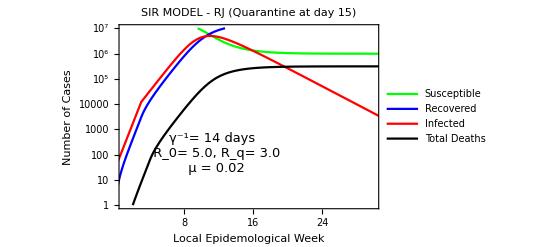

```mathematica
(*SIR + Quarantine*)

Clear[γ,β,R0,pop,solution,Sus,Inf,Rec,Death,β2,R02]
Needs["PlotLegends`"]
γ=1/(14/7);
μ=0.02;
R0[t_]:=Piecewise[{{5.00,t<3},{3.0,t≥3 &&t<3},{3.0,t≥3}}];
β[t_]:=γ*R0[t];
pop=16500000;
solution=NDSolve[{Sus'[t]==-β[t]*Inf[t]*Sus[t]/pop,Inf'[t]==β[t] *Inf[t] Sus[t]/pop-γ Inf[t],Rec'[t]==γ Inf[t],Death[t]==μ*( Rec[t]),Sus[0]==pop,Inf[0]==30,Rec[0]==0,Death[0]==0},{Inf,Sus,Rec,Death},{t,-10,30}];



LogPlot[Evaluate[{Sus[t],Rec[t],Inf[t],Death[t-1]}/.%],{t,0,300},PlotRange->{{1,30},{1,10000000}},PlotPoints->640,PlotLegends->Placed[{"Susceptible","Recovered","Infected","Total Deaths"},{0.75,0.27}],GridLines->Automatic,PlotStyle->{{Green},{Blue},{Red},{Black}},TicksStyle->Directive[FontSize-> 15],Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[Black,12],Epilog->Text[Style["γ^-1= 14 days\n  R_0= 5.0, R_q= 3.0\n  μ = 0.02",13],Scaled[{0.36,0.3}]],PlotLabel->"SIR MODEL - RJ (Quarantine at day 15)",FrameLabel->{"Local Epidemological Week","Number of Cases"},LabelStyle->Directive[Black, 12]]
```

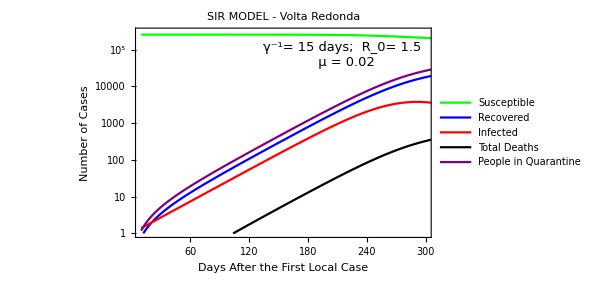

```mathematica
SIR-X MODEL;

-Graphics-;

Clear[γ,β,R0,pop,solution,Sus,Inf,Rec,Death,X,κ0,κ]
Needs["PlotLegends`"]
γ=1/15;
β=γ*R0;
μ=0.02;
R0=3.0;
κ0=0.0; (*Social Distancing*)
κ=0.1;(*Quarantine Measurements for Infecteds*)
pop=257000;
solution=NDSolve[{Sus'[t]==-β*Inf[t]*Sus[t]/pop-κ0* Sus[t],Inf'[t]==β Inf[t] Sus[t]/pop-γ Inf[t]-κ0 Inf[t]-κ Inf[t],Rec'[t]==γ Inf[t]+κ0*Sus[t],Death[t]==μ*( Rec[t]),X'[t]==(κ+κ0) Inf[t],Sus[0]==pop,Inf[0]==1,Rec[0]==0,Death[0]==0, X[0]==0},{Inf,Sus,Rec,Death, X},{t,-50,700}];





LogPlot[Evaluate[{Sus[t],Rec[t],Inf[t],Death[t-6],X[t]}/.%],{t,10,700},PlotRange->{{10,300},{1,300000}},PlotPoints->640,PlotLegends->Placed[{"Susceptible","Recovered","Infected","Total Deaths","People in Quarantine"},{0.48,0.27}],GridLines->Automatic,PlotStyle->{{Green},{Blue},{Red},{Black},{Purple}},TicksStyle->Directive[FontSize-> 15],Frame->True,FrameTicks->Automatic,FrameTicksStyle->Directive[Black,12],Epilog->Text[Style["γ^-1= 15 days;  R_0= 1.5\n  μ = 0.02",13],Scaled[{0.7,0.87}]],PlotLabel->"SIR MODEL - Volta Redonda",FrameLabel->{"Days After the First Local Case","Number of Cases"},LabelStyle->Directive[Black, 12]]
```